```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-k-n.wdx"];
f1=(-I)*Query[1,1]@a;
```

```mathematica
nf1=f1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
```

```mathematica
ref1[x_]=Simplify[nf1/.{y->x}];
```

```mathematica
f[x_]=Hold[NIntegrate[ref1[x],{k3,0,∞},{θ,0,2π},WorkingPrecision->10]]
```

Hold[NIntegrate[ref1[x],{k3,0,∞},{θ,0,2 π},WorkingPrecision→10]]

```mathematica
ReleaseHold[f[0.12]]
```

-0.266724028

```mathematica
l1=Table[{x,ReleaseHold[f[x]]},{x,-0.189,0.189,0.001}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
f2=(-I)*Query[2,1]@a;
nf2=f2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
```

```mathematica
ref2[x_]=Simplify[nf2/.{y->x}];
```

```mathematica
ff[x_]=Hold[NIntegrate[ref2[x],{k3,0,∞},{θ,0,2π},WorkingPrecision->10]];
```

```mathematica
l2=Table[{x,ReleaseHold[ff[x]]},{x,0.2,1,0.001}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

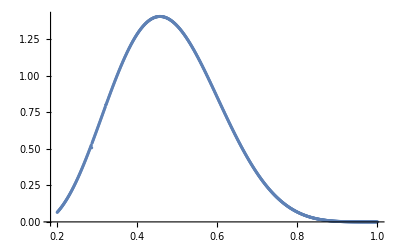

```mathematica
ListPlot[l2]
```

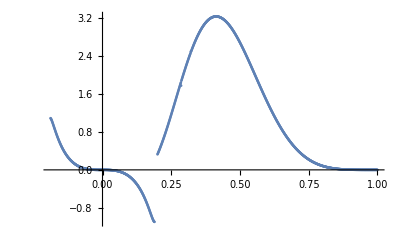

```mathematica
ListPlot[Join[l1,l2]]
```

```mathematica
l3=Table[{x,ReleaseHold[f[x]]},{x,-0.2,-0.19,0.00001}];
l4=Table[{x,ReleaseHold[f[x]]},{x,0.19,0.2,0.00001}];
```

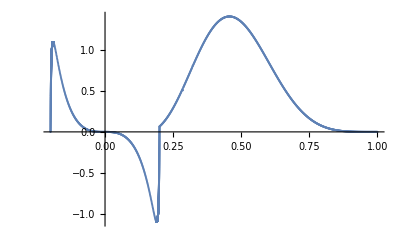

```mathematica
ListPlot[Join[l3,l1,l4,l2]]
```